FittedModel[0.000202672 x^4-0.00313354 x^3+0.0156182 x^2-0.00933617 x+0.00164822]

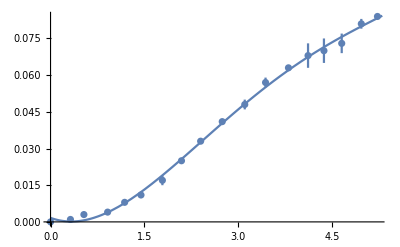

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00164822 | 0.00135834 | 1.2134 | 0.246562
x | -0.00933617 | 0.0038562 | -2.42108 | 0.0308426
x^2 | 0.0156182 | 0.00313691 | 4.97886 | 0.000252207
x^3 | -0.00313354 | 0.000913025 | -3.43205 | 0.00445922
x^4 | 0.000202672 | 0.0000864113 | 2.34543 | 0.0355274

```mathematica
Needs["ErrorBarPlots`"]
magnet =  {{5.223,0.581, 0.001},{4.965, 0.584, 0.002},{4.652, 0.592, 0.004},{4.368,0.595,0.005},{4.114,0.597,0.005},{3.801,0.602,0.001},{3.435,0.608,0.002},{3.103,0.617,0.002},{2.743,0.624,0.001},{2.398,0.632,0.001},{2.092,0.640,0.001},{1.787,0.648,0.002},{1.445,0.654,0.001},{1.184,0.657,0.001},{0.912,0.661,0.001},{0.533,0.662,0.001},{0.318,0.664,0.001},{0.000,0.665,0.001}};
magnetError ={{#[[1]],0.665- #[[2]]},ErrorBar[#[[3]]]} &/@magnet;
lf = LinearModelFit[Map[{#[[1,1]], #[[1,2]]}&, magnetError],{1,x, x^2,x^3, x^4}, x] 
Show[ErrorListPlot[magnetError], Plot[lf, {x, 0, 5}], Plot[lf[x], {x, 0, 5.3}]]
lf["ParameterTable"]
```

FittedModel[0.734944 erfc(4.94153 x-0.377655)+0.0123943]

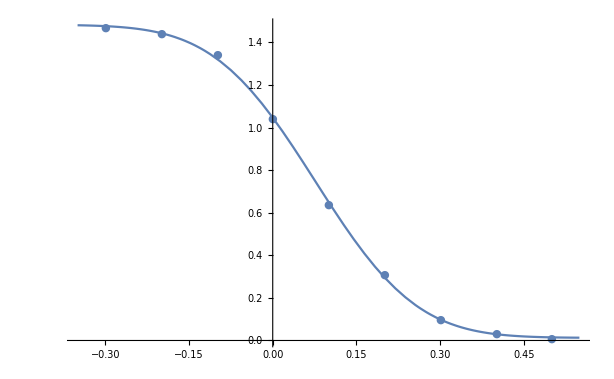

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.734944 | 0.00741214 | 99.1541 | 1.97824×10^-9
B | 4.94153 | 0.132642 | 37.2548 | 2.62451×10^-7
CC | 0.377655 | 0.0175903 | 21.4694 | 4.06591×10^-6
DD | 0.0123943 | 0.00886748 | 1.39773 | 0.221044

```mathematica
beampower = {{39.7, 1.47},{39.8, 1.44},{39.9,1.34},{40,1.04},{40.1,0.64},{40.2,0.31},{40.3,0.1},{40.4, 0.03},{40.5, 0.01}};
beampowerError = Map[{{#[[1]], #[[2]]},ErrorBar[0.01]} &,beampower];
nlm = NonlinearModelFit[Map[{#[[1]]-40,#[[2]]} &, beampower],A*Erfc[B*x-CC]+DD, {A,B,CC,DD},x]
Show[Plot[nlm[x],{x,-0.35,0.55}],ErrorListPlot[Map[{{#[[1, 1]] - 40, #[[1, 2]]},#[[2]]} &, beampowerError],PlotMarkers->{Automatic,Tiny}]]
nlm["ParameterTable"]
```

FittedModel[0.734944 erfc(4.94153 x-198.039)+0.0123943]

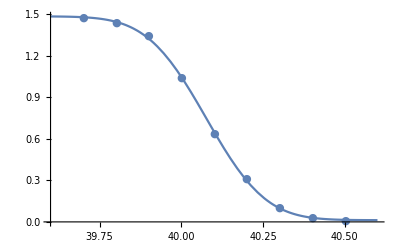

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.734944 | 0.00741214 | 99.1541 | 1.97824×10^-9
B | 4.94153 | 0.132642 | 37.2548 | 2.62451×10^-7
CC | 198.039 | 5.31686 | 37.2474 | 2.62711×10^-7
DD | 0.0123943 | 0.00886748 | 1.39773 | 0.221044

```mathematica
nlm2 = NonlinearModelFit[Map[{#[[1]],#[[2]]} &, beampower],A*Erfc[B*x-CC]+DD, {{A,0.7},{B,4.94},{CC,193.6},{DD,0.01}},x]
Show[Plot[nlm2[x],{x,39.6,40.6}],ErrorListPlot[Map[{{#[[1, 1]] , #[[1, 2]]},#[[2]]} &, beampowerError],PlotMarkers->{Automatic,Tiny}]]
nlm2["ParameterTable"]
```